# Rania —PS 10 (2.25.2025)

## EIWL3 Sections 26, 27, and 28

## Section 26

Some notes because Wolfram didn’t really:
/@: apply the previous thing to all elements in list following it
&: indicates the previous is a pure function
#: “slot” in which element is put  (if it’s followed /@ it will each element into the list)
EXAMPLE:
Rotate[#, 90 degree] &/@{“one”, “two”, “three”]  -> Rotate[one, 90 degree], Rotate[two, 90 degree]...
vs. 
Rotate[“hello”, #] &/@[30 deg, 90 deg, 80 deg] -> Rotate[“hello”, 30 degree], Rotate[“hello”, 90 degree]...
#: can also be used to pair
{#, ColorNegate[#]}&/@{Red, Blue, Green}

```mathematica
(*26.1 Use Range and a pure function to create a list of the first 20 squares.*)
Power[#,2]&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
(*26.2 A list of the result of blending yellow,green and blue with red*)
Blend[{#,Red}]&/@ {Yellow, Green, Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
(*26.3 Generate a list of framed columns containing the uppercase and lowercase versions of each letter of the alphabet.*)
Framed[Column[{ToUpperCase[#], #}]]&/@ Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
(*26.4 A list of letters of the alphabet,in random colors,with frames having random background colors.*)
Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

EntityValue::conopen: Using EntityValue requires internet connectivity. Please check your network connection. You may need to configure your firewall program or set a proxy in the Internet Connectivity tab of the Preferences dialog.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

EntityValue::outdcache: Using potentially outdated cached values.

EntityValue::conopen: Using EntityValue requires internet connectivity. Please check your network connection. You may need to configure your firewall program or set a proxy in the Internet Connectivity tab of the Preferences dialog.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

EntityValue::outdcache: Using potentially outdated cached values.

EntityValue::conopen: Using EntityValue requires internet connectivity. Please check your network connection. You may need to configure your firewall program or set a proxy in the Internet Connectivity tab of the Preferences dialog.

General::stop: Further output of EntityValue::conopen will be suppressed during this calculation.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

General::stop: Further output of EntityValue::nodat will be suppressed during this calculation.

EntityValue::outdcache: Using potentially outdated cached values.

General::stop: Further output of EntityValue::outdcache will be suppressed during this calculation.






France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

Syntax::bktmop: Expression "Framed[Grid[Table[{#,CountryData[#,Flag]},1]]]&/@EntityList[EntityClass[Country,GroupOf5]])" has no opening "(".

```mathematica
(*26.5 A table of G5 countries,together with their flags,and arrange the result in a fully framed grid.*)
Grid[{#,EntityValue[#,"Flag"]}&/@EntityList[EntityClass["Country","GroupOf5"]],Frame->Automatic]
(*Framed[Grid[Table[{#,CountryData[#,"Flag"]},1]]]&/@EntityList[EntityClass["Country","GroupOf5"]])*
```

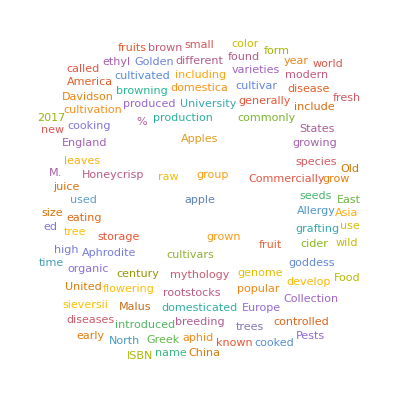
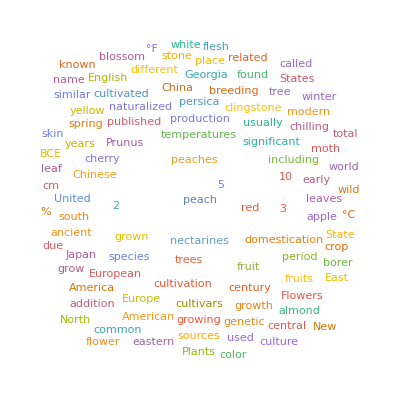
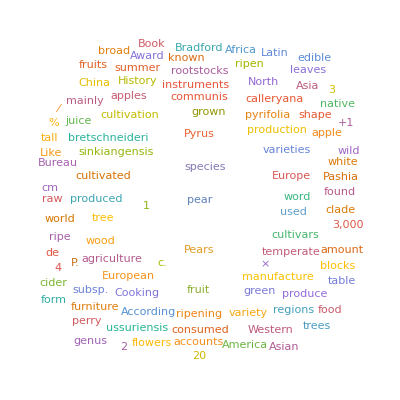

```mathematica
(**)
WordCloud[WikipediaData[#]]&/@{"apple", "peach", "pear"}
```

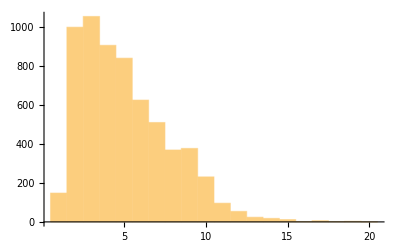
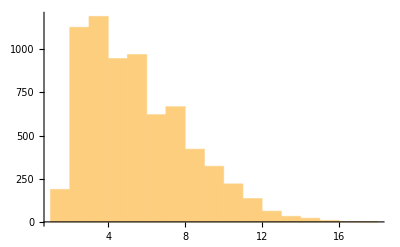
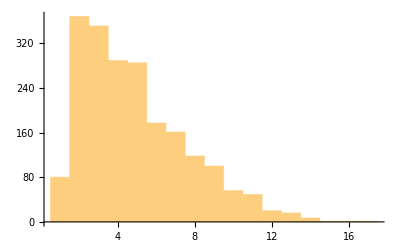

```mathematica
(* 26.7 List of histograms of the word lengths in Wikipedia articles on apple,peach and pear.*)
Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach", "pear"}
```

```mathematica
(*26.8 A list of maps of Central America,highlighting each country in turn*)GeoListPlot[#, GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Section 27

```mathematica
(*27.1 Make a list of the results of nesting Blur up to 10 times,starting with a rasterized size-30 “X”*)
NestList[Blur,  Rasterize[Style["A",20]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*27.2 Start with x,then make a list by nestedly applying Framed up to 10 times,using a random background color each time*)
NestList[Framed[#, Background->RandomColor[]] &,x,10]
(*sorta confused of using # without /@*)
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
(*27.3 Start with a size-50 “A”,then make a list of nestedly applying a frame and a random rotation 5 times*)

NestList[Framed[Rotate[#, RandomReal[]]]&, Style["A", 50],5]
```

{A,A,A,A,A,A}

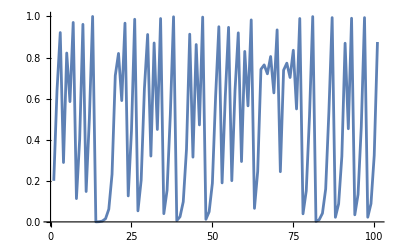

```mathematica
(*27.4 Make a line plot of 100 iterations of the logistic map iteration 4 #(1-#)&,starting from 0.2*)
ListLinePlot[NestList[4 #(1-#)&, 0.2, 100]]
```

```mathematica
(*27. 5 Find the numerical value of the result from 30 iterations of 1+1/#& starting from 1.*)
N[Nest[1+1/# &, 1, 30]]
```

1.61803

```mathematica
(*27. 6 Create a list of the first 10 powers of 3 (starting at 0) by nested multiplication.*)
NestList[3#&, 1, 10]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
(* 27.7 Make a list of the result of nesting the (Newton’s method) function (#+2/#)/2& up to 5 times starting from 1.0,and then subtract sqrt 2 from all the results *)
NestList[(#+2/#)/2&, 1.0, 5] - Sqrt[2]
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

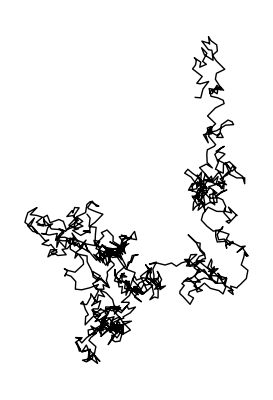

```mathematica
(*27. 8 Make graphics of a 1000-step 2D random walk which starts at {0,0},and in which at each step a pair of random numbers between−1 and+1 are added to the coordinates.*)
Graphics[Line[Accumulate[RandomReal[{-1,1},{1000,2}]]]]
```

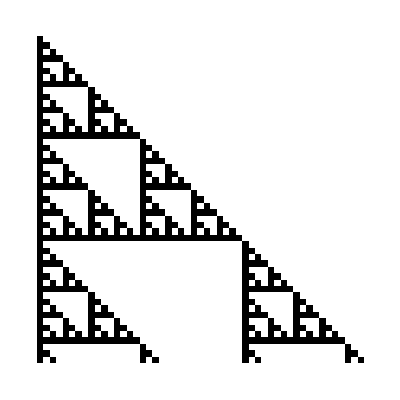

```mathematica
(*27.9 Make an array plot of 50 steps of Pascal’s triangle modulo 2 by starting from {1} and nestedly joining {0} at the beginning and at the end,and adding these results together modulo 2 *)
ArrayPlot[NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]]
```

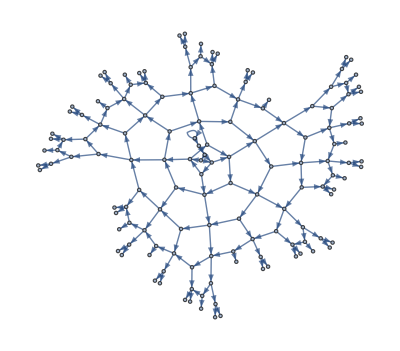

```mathematica
(*27.10 Generate a graph by starting from 0,then nestedly 10 times connecting each node with value n to ones with values n+1 and 2n.*)
NestGraph[{#+1,2#}&,0,10]
```

```mathematica
(* 27.11 Generate a graph obtained by nestedly finding bordering countries starting from the United States,and going 4 iterations.*)
NestGraph[#["BorderingCountries"]&,Entity["Country","UnitedStates"],4,VertexLabels->All]
```

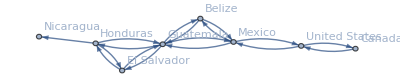

## Section 28

== conditional (True/false)
 && represents “and”
|| represents “or” 
! represents “not”

```mathematica
(*28. 1 Test whether 123^321 is greater than 456^123*)
123^321 > 456^123
```

True

```mathematica
(*28.2 Get a list of numbers up to 100 whose digits add up to less than 5.*)
Select[Range[100],DigitSum[# ] <=5 &]
```

{1,2,3,4,5,10,11,12,13,14,20,21,22,23,30,31,32,40,41,50,100}

```mathematica
(*28.3 Make a list of the first 20 integers, with prime numbers styled red.*)
If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
(*28.4 Find words in WordList[] that both begin and end with the letter “p”.*)
Select[WordList[],StringTake[#,1]==StringTake[StringReverse[#],1]=="p"&]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,peep,penmanship,pep,pickup,pileup,pip,plop,plump,polyp,pomp,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

```mathematica
(*28.5 Make a list of the first 100 primes,keeping only ones whose last digit is less than 3.*)
Select[Prime[Range[100]],Last[IntegerDigits[#]]<3&]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

```mathematica
(*28. 6 Find Roman numerals up to 100 that do not contain “I”*)
Select[RomanNumeral[Range[100]], ! MemberQ[Characters[#],"I" ]&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
(*28.7 Get a list of Roman numerals up to 1000 that are palindromes.*)
Select[RomanNumeral[Range[1000]], StringReverse[#]== # &]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

```mathematica
(*28.8Find names of integers up to 100 that begin and end with the same letter.*)
Select[IntegerName[Range[100]], StringTake[#,1]== Last[Characters[#]]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
(*28.9 Get a list of words longer than 15 characters from the Wikipedia article on words.*)
Select[TextWords[WikipediaData["Words"]],StringLength[#]>15&]
```

{yibi-jarran-gabun,yibi-gabun-jarran,orthographically,multiple-morpheme,Proto-Indo-European,978-0-08-044854-1}

```mathematica
(*28.10 Starting from 1000,divide by 2 if the number is even,and compute 3#+1& if the number is odd;do this repeatedly 200 times (Collatz problem)*)
NestList[If[EvenQ[#],#/2,3#+1]&,1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

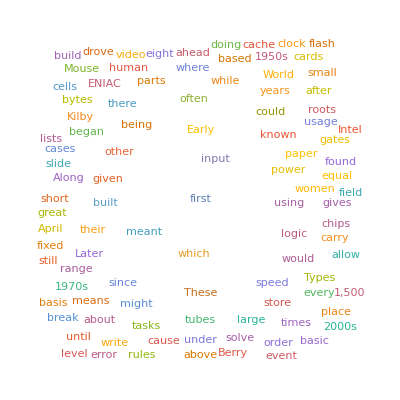

```mathematica
(*28.11 Make a word cloud of 5-letter words in the Wikipedia article on computers*)
WordCloud[Select[TextWords[WikipediaData["computers"]], StringLength[#]==5 &]]
```

```mathematica
(*28.12Find words in WordList[] whose first 3 letters are the same as their last 3 read backward,but where the whole string is not a palindrome.*)
Select[WordList[],StringLength[#]>=3&&#!=StringReverse[#]&&StringTake[#,3]==StringTake[StringReverse[#],3]&]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
(*8.13Find all 10-letter words in WordList[] for which the total of LetterNumber values is 100.*)
Select[Select[WordList[],StringLength[#]==10&],Total[LetterNumber/@Characters[#]]==100&]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}